```mathematica
Table[Range[2],5]
```

{{1,2},{1,2},{1,2},{1,2},{1,2}}

```mathematica
Table[RandomInteger[1],5]
```

{0,1,0,0,1}

```mathematica
AbsoluteTiming[For[i=1,i≤100,i++,AppendTo[s,ArrayReshape[RandomSample[Range[100]],{10,10}]]]][[1]]
```

0.001025

```mathematica
AbsoluteTiming[RandomInteger[100,{100,10,10}]][[1]]
```

0.000102

```mathematica
Table[]
```

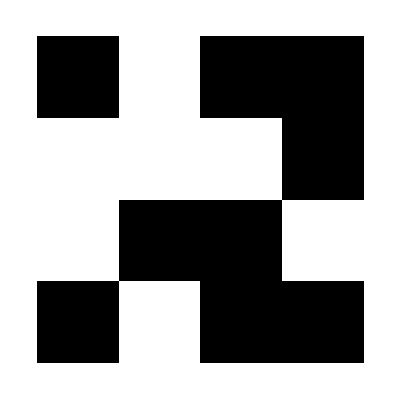
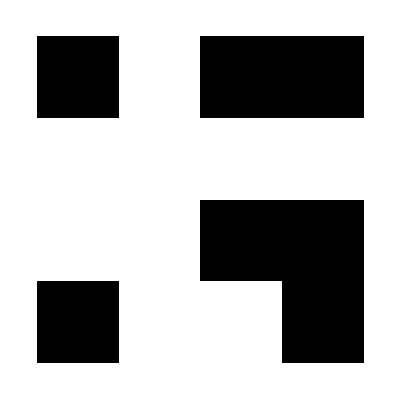
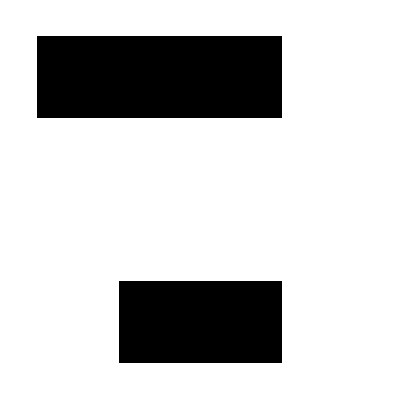
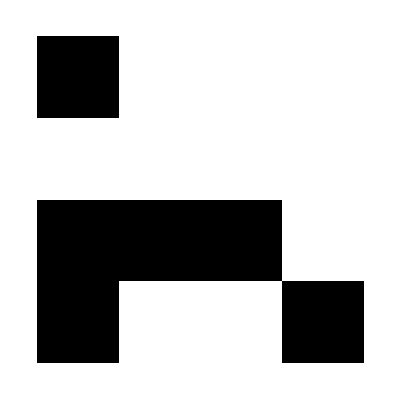
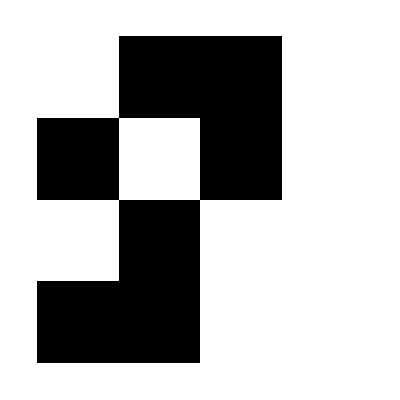
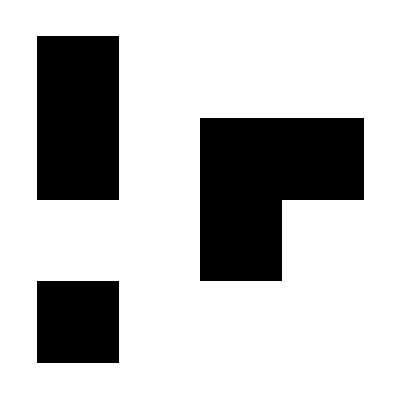
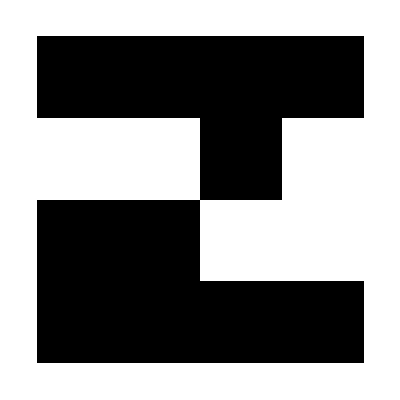
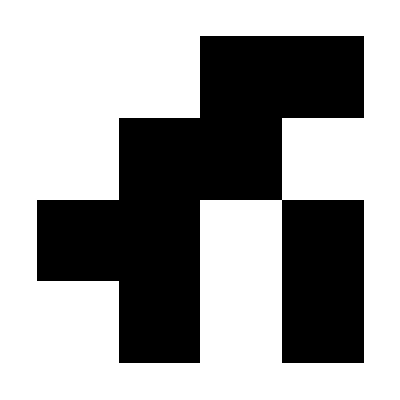

```mathematica
SeedRandom[1242345];ArrayPlot/@RandomInteger[1,{10,4,4}]
```

```mathematica
(#1+#2)&[#,2]&/@{1,2,3,x,p}
```

{3,4,5,2+x,2+p}